## Giuseppe’s proposal

```mathematica
d=.
c=.
α=.
T=.
V[m_,c_]= Sum[PDF[PoissonDistribution[c  ],k](1-(1- m)^k),{k,1,∞}]
v[m_,c_]= Sum[PDF[PoissonDistribution[c  ],k] k/c(1-(1- m)^(k-1)),{k,1,∞}]
m[v_,d_,T_]= Sum[PDF[PoissonDistribution[d],k] k/d(1-(1- T v)^(k-1)),{k,1,∞}]
```

ⅇ^(-c-c (-1+m)) (-1+ⅇ^(c+c (-1+m)))

ⅇ^(-c m) (-1+ⅇ^(c m))

ⅇ^(-d T v) (-1+ⅇ^(d T v))

```mathematica
Manipulate[Plot[{v[m[x,d,T],c]-x,m[v[x,c],d,T]-x},{x,0,1}],{T,0,1},{d,0,6},{c,0,6}]
```

```mathematica
c = 4;
d = 4;
T= 0.1;
V[x,c]/.NSolve[m[v[x,c],d,T]-x==0,x,Reals][[-1]]
```

0.540598

```mathematica
NSolve[m[v[x,c,T],d]-x==0,x,Reals][[-1]]
```

{x→0.540598}

```mathematica
c=2;
Sum[PDF[PoissonDistribution[c  -1], k - 1] k^2, {k, 1, ∞}]
```

5

```mathematica
-1+c+c^2
```

```mathematica
Sum[PDF[PoissonDistribution[c  -1], k - 1] k, {k, 1, ∞}]
```

2

```mathematica
Max[Eigenvalues[{{0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 1, 0}, {0, 0, 0, 5, 1, 1}, {5/8T, 5/8T, 5/2T, 0, 0, 0}, {0, 1/2T, 1T, 0, 0, 0}, {0, 0, 5T, 0, 0, 0}}]]
```

1.38571

```mathematica
Eigenvalues[{{0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 1, 0}, {0, 0, 0, 5, 1, 1}, {5/8T, 5/8T, 5/2T, 0, 0, 0}, {0, 1/2T, 1T, 0, 0, 0}, {0, 0, 5T, 0, 0, 0}}]
```

{-1.38571,1.38571,0.205703,-0.205703,-1.03636×10^-17,0.}

```mathematica
(1/2)T
```

0.05

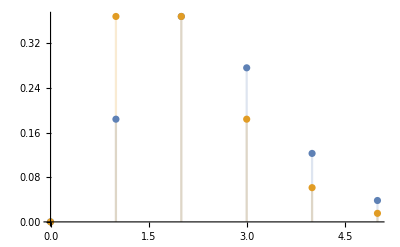

```mathematica
c=1;
DiscretePlot[{PDF[PoissonDistribution[c  ],k-1] k/(c+1),PDF[PoissonDistribution[c  ],k-1]},{k,0,5,1}]
```

```mathematica
c=.;
Simplify[PDF[PoissonDistribution[c  ],k-1] k/(c+1),Assumptions->k>1]
```

(c^(-1+k) ⅇ^-c k)/((1+c) (-1+k)!)

1

## Reimer’s formulation

```mathematica
d=.
c=.
α=.
p=.
v[m_,c_,p_]= Sum[PDF[PoissonDistribution[c  ],k-1] k/(c+1)(1-(1-p m)^k),{k,1,∞}]
m[v_,d_]= Sum[PDF[PoissonDistribution[d],k-1] k/(d+1) (k-1)/d v,{k,1,∞}]
```

(ⅇ^(-c m p) (-1-c+ⅇ^(c m p)+c ⅇ^(c m p)+m p+2 c m p-c m^2 p^2))/(1+c)

((2+d) v)/(1+d)

```mathematica
d = 1;
c=1;
Manipulate[Plot[v[m[x,d,p],c]-x,{x,0,1}],{p,0,1},{d,0,6},{c,0,6}]
```

```mathematica
FortranForm[v[m[x,d,T],c]-x//.{1. y_->y,E^x_->exp[x],α->alpha}]
```

-x + (exp(-((c*exp(-(d*T*x))*(-1 - d + d*T*x + exp(d*T*x) + d*exp(d*T*x)))/(1 + d)))*
     -     (-1 - c + (c*exp(-(d*T*x))*(-1 - d + d*T*x + exp(d*T*x) + d*exp(d*T*x)))/(1 + d) + 
     -       exp((c*exp(-(d*T*x))*(-1 - d + d*T*x + exp(d*T*x) + d*exp(d*T*x)))/(1 + d)) + c*exp((c*exp(-(d*T*x))*(-1 - d + d*T*x + exp(d*T*x) + d*exp(d*T*x)))/(1 + d)))
     -     )/(1 + c)

```mathematica
v[m[x,d,p],c]-x
```

-x+(ⅇ^(-(c ⅇ^(-d p x) (-1-d+ⅇ^(d p x)+d ⅇ^(d p x)+d p x))/(1+d)) (-1-c+ⅇ^((c ⅇ^(-d p x) (-1-d+ⅇ^(d p x)+d ⅇ^(d p x)+d p x))/(1+d))+c ⅇ^((c ⅇ^(-d p x) (-1-d+ⅇ^(d p x)+d ⅇ^(d p x)+d p x))/(1+d))+(c ⅇ^(-d p x) (-1-d+ⅇ^(d p x)+d ⅇ^(d p x)+d p x))/(1+d)))/(1+c)

```mathematica
m[v[x,c],d,p]-x
```

-x+(ⅇ^(-(d ⅇ^(-c x) p (-1-c+ⅇ^(c x)+c ⅇ^(c x)+c x))/(1+c)) (-1-d+ⅇ^((d ⅇ^(-c x) p (-1-c+ⅇ^(c x)+c ⅇ^(c x)+c x))/(1+c))+d ⅇ^((d ⅇ^(-c x) p (-1-c+ⅇ^(c x)+c ⅇ^(c x)+c x))/(1+c))+(d ⅇ^(-c x) p (-1-c+ⅇ^(c x)+c ⅇ^(c x)+c x))/(1+c)))/(1+d)

```mathematica
FortranForm[m[v[x,c,T],d,T]-x//.{1. y_->y,E^x_->exp[x],α->alpha}]
```

-x + (exp(-((d*T*exp(-(c*T*x))*(-1 - c + c*T*x + exp(c*T*x) + c*exp(c*T*x)))/(1 + c)))*
     -     (-1 - d + (d*T*exp(-(c*T*x))*(-1 - c + c*T*x + exp(c*T*x) + c*exp(c*T*x)))/(1 + c) + 
     -       exp((d*T*exp(-(c*T*x))*(-1 - c + c*T*x + exp(c*T*x) + c*exp(c*T*x)))/(1 + c)) + 
     -       d*exp((d*T*exp(-(c*T*x))*(-1 - c + c*T*x + exp(c*T*x) + c*exp(c*T*x)))/(1 + c))))/(1 + d)

```mathematica
Manipulate[Plot[{ⅇ^(-c m) (-1+ⅇ^(c m)+m),m},{m,0,1}],{c,0,3}]
```